#### Evaluation of Sudakov radiator

```mathematica
idycoupling = {as->a[μR]/csi*(1-a[μR]*β1/β0*Log[csi]/csi+(a[μR]*β1/β0*Log[csi]/csi)^2-a[μR]^2*(β1^2/β0^2*(Log[csi]-a[μR]*β0*t)/csi^2+β2*a[μR]*t/csi^2))/.csi->1-ρ/.t-> -ρ/a[μR]/β0(*a[μR]*β0*t/.t->2 Log[μ/μR]*)}
```

{as→(a[μR] (1-(β1 a[μR] Log[1-ρ])/(β0 (1-ρ))+(β1^2 a[μR]^2 Log[1-ρ]^2)/(β0^2 (1-ρ)^2)-a[μR]^2 (-(β2 ρ)/(β0 (1-ρ)^2)+(β1^2 (ρ+Log[1-ρ]))/(β0^2 (1-ρ)^2))))/(1-ρ)}

```mathematica
asCMW = A1 as (1+as/(2 Pi) A2/A1 + as^2/(2 Pi)^2 A3/A1)/.idycoupling/.a[μR]->α
```

1/(1-ρ)A1 α (1-(α β1 Log[1-ρ])/(β0 (1-ρ))+(α^2 β1^2 Log[1-ρ]^2)/(β0^2 (1-ρ)^2)-α^2 (-(β2 ρ)/(β0 (1-ρ)^2)+(β1^2 (ρ+Log[1-ρ]))/(β0^2 (1-ρ)^2))) (1+(A2 α (1-(α β1 Log[1-ρ])/(β0 (1-ρ))+(α^2 β1^2 Log[1-ρ]^2)/(β0^2 (1-ρ)^2)-α^2 (-(β2 ρ)/(β0 (1-ρ)^2)+(β1^2 (ρ+Log[1-ρ]))/(β0^2 (1-ρ)^2))))/(2 A1 π (1-ρ))+(A3 α^2 (1-(α β1 Log[1-ρ])/(β0 (1-ρ))+(α^2 β1^2 Log[1-ρ]^2)/(β0^2 (1-ρ)^2)-α^2 (-(β2 ρ)/(β0 (1-ρ)^2)+(β1^2 (ρ+Log[1-ρ]))/(β0^2 (1-ρ)^2)))^2)/(4 A1 π^2 (1-ρ)^2))

```mathematica
(* integrate the "collinear" term: *)
```

```mathematica
ker1 = (asCMW/Pi*(1/2 ρ/α/β0)+as/Pi A1( B1/A1/2+ as/Pi B2/A1/4))/α/β0/.idycoupling/.a[μR]->α;
int1=Integrate[ker1,ρ];
int1=(int1/.ρ->0)-Limit[int1,ρ->  λ,Assumptions->{λ>0,α>0,β0<0}];
```

```mathematica
R1= Series[int1,{α,0,1}]//FullSimplify;
```

```mathematica
(* integrate the "soft" term: *)
```

```mathematica
ker2 = asCMW/Pi (-1/2  ρ/α/β0 +λ/α/β0)/α/β0;
int2 = Integrate[ker2,ρ];
int2 = Limit[int2,ρ-> λ,Assumptions->{λ>0}]-Limit[int2,ρ-> 2λ,Assumptions->{λ>0}];
```

```mathematica
R2 = Series[int2,{α,0,1}]//FullSimplify;
```

```mathematica
(* obtain the Sudakov radiator R *)
```

```mathematica
R = R1+R2;
```

```mathematica
(* restore resummation scale dependence *)
```

```mathematica
R = Series[R,{α,0,1}];
```

```mathematica
h1[λ_] = Collect[SeriesCoefficient[R,{α,0,-1}]//Expand,A1,FullSimplify]/λ β0
```

(A1 ((-1+2 λ) Log[1-2 λ]-2 (-1+λ) Log[1-λ]))/(2 π β0 λ)

#### Anomalous dimensions and constants

```mathematica
constants={
(*beta function*)
β0->1/(4π)(-4/3*nf*Tf+11/3*Ca),
β1->1/(π)^2(17*Ca^2-5*Ca*nf-3*Cf*nf)/24,
β2->1/(4π)^3(325/54*nf^2-5033/18*nf+2857/2),
A1->2Cf,
A2-> Cf((67/9-π^2/3)Ca-20/9 Tf nf),
B1-> -3 Cf,
(*Tf*)
Tf->1/2,
Ca->3,
Cf->4/3,
nf->5,
as->0.118 (* strong coupling *)
};
```

#### exp[-R(τ)]

```mathematica
h1[λ_]=(A1 ((-1+2 λ) Log[1-2 λ]-2 (-1+λ) Log[1-λ]))/(2 π β0 λ);
```

```mathematica
Rp[L_]=-(D[X h1[as β0 X],X])/.X->L//.constants;
```

```mathematica
Subscript[Σ, max][L_] = Exp[L h1[as β0 L]]//.constants;
```

#### Analytic Result for the transfer function

```mathematica
Fanalytic[L_] = Exp[-EulerGamma Rp[L]]/Gamma[1+Rp[L]];
```

#### Computation of the transfer function (efficient way)

number of events to generate, and IR cutoff

```mathematica
Nevents = 1000;  
ln1Cutoff=10;
```

Array containing observable’s values at which the cross section is computed

```mathematica
v=Array[# 1/100&,30]
```

{1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10}

start with ln1zeta = Log[1/ζ_i] = Log[1/ζ_1]=0, only the first emission is present

```mathematica
F=Array[0&,Length[v]];
errF=Array[0&,Length[v]];
AbsoluteTiming[For[ibin=1,ibin≤ Length[v],ibin++,
For[iev=1,iev≤ Nevents, iev++,
ln1zeta= 0;
zetaSum = 0;
nems=0;
While[ln1zeta < ln1Cutoff,
zetaSum = zetaSum + Exp[-ln1zeta];
nems = nems + 1;
r=0;
While[r == 0,r=RandomReal[]];
u = -Log[r]/Rp[Log[1/v[[ibin]]]];
ln1zeta = ln1zeta + u;
];
F[[ibin]]= F[[ibin]]+ Exp[-Rp[Log[1/v[[ibin]]]] Log[zetaSum]]/Nevents;
errF[[ibin]]= errF[[ibin]]+ (Exp[-Rp[Log[1/v[[ibin]]]] Log[zetaSum]])^2/Nevents;
];
errF[[ibin]] = Sqrt[Abs[errF[[ibin]]-F[[ibin]]^2]]/Nevents;]]
```

{2.41126,Null}

Compare to the analytic solution

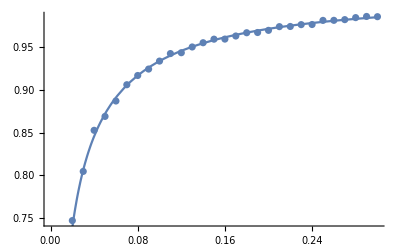

```mathematica
Histo=Table[{v[[i]],F[[i]]},{i,1,Length[v]}];
Show[{ListPlot[Histo],Plot[Fanalytic[Log[1/τ]],{τ,0,v[[Length[v]]]}]}]
```

#### Computation of the transfer function (inefficient way)

number of events to generate, and IR cutoff

```mathematica
Nevents = 1000;  
ln1Cutoff=10;
```

Array containing observable’s values at which the cross section is computed

```mathematica
v=Array[# 1/100&,30]
```

{1/100,1/50,3/100,1/25,1/20,3/50,7/100,2/25,9/100,1/10,11/100,3/25,13/100,7/50,3/20,4/25,17/100,9/50,19/100,1/5,21/100,11/50,23/100,6/25,1/4,13/50,27/100,7/25,29/100,3/10}

```mathematica
v=Array[# 1/1000&,100]//N
```

{0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,0.1}

start with ln1zeta = Log[1/ζ_i] = Log[1/ζ_1]=0, only the first emission is present

```mathematica
F=Array[0&,Length[v]];
AbsoluteTiming[For[ibin=1,ibin≤ Length[v],ibin++,
For[iev=1,iev≤ Nevents, iev++,
ln1zeta= 0;
zetaSum = 0;
nems=0;
(* generate first emission *)
r=0;
While[r == 0,r=RandomReal[]];
ln1zeta= -Log[r]/Rp[Log[1/v[[ibin]]]];
While[ln1zeta < ln1Cutoff,
zetaSum = zetaSum + Exp[-ln1zeta];
nems = nems + 1;
r=0;
While[r == 0,r=RandomReal[]];
u = -Log[r]/Rp[Log[1/v[[ibin]]]];
ln1zeta = ln1zeta + u;
];
If[zetaSum ≤ 1, F[[ibin]]= F[[ibin]]+ 1/Nevents];
]]]
```

{8.77967,Null}

Compare to the analytic solution

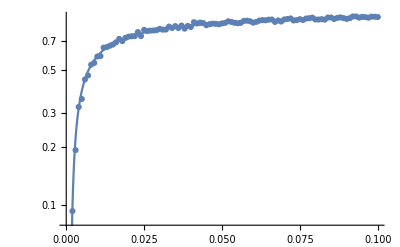

```mathematica
Histo=Table[{v[[i]],F[[i]]},{i,1,Length[v]}];
Show[{ListLogPlot[Histo,PlotRange->All],LogPlot[Fanalytic[Log[1/τ]],{τ,0,v[[Length[v]]]},PlotRange->All]}]
```

#### Thrust resummed distribution and comparison to fixed order

```mathematica
Subscript[Σ, res][τ_] := Subscript[Σ, max][Log[1/τ]] Fanalytic[Log[1/τ]];
```

compute the differential distribution and compare to the fixed-order at LO (from Ellis-Stirling-Webber Eq. 3.44)

```mathematica
Subscript[dΣ, res][τ_]:=D[Subscript[Σ, res][x],x]/.x->τ
```

```mathematica
Subscript[dΣ, LO][τ_] := Cf as/(2 Pi) (2 (3 T^2-3 T+2)/(T(1-T))Log[(2T-1)/(1-T)]-3 (3T -2)(2-T)/(1-T)) /.T->1-τ//.constants
```

```mathematica
Plot[{Subscript[dΣ, LO][τ],Subscript[dΣ, res][τ]},{τ,0.001,1/3},PlotRange->{{0,40}},AxesLabel->{"τ","1/σdσ/(d τ)"},PlotLegends->Placed[{"LO distribution","Resummed distribution"},{Center}]]
```

-Graphics-